# Plots Across Dataset for Specific Run

## Data Selection

```mathematica
(*Set directory paths.*)
SetDirectory[NotebookDirectory[]];
plotsDir= "kl_div_plots";
dataDir = "mlflow_data";
```

```mathematica
(*Set the name of the experiment.*)
experiments =FileNameTake/@(FileNames[All, dataDir]);
experimentName =.;
PopupMenu[Dynamic[experimentName],experiments]
```

```mathematica
(*Get the experiment directory and the names of all the runs in that directory.*)
experimentDir=FileNameJoin[{dataDir, experimentName}];
runDirs = FileNames[All, experimentDir];
runNames = FileNameTake/@runDirs;

(*Select which run to plot.*)
desiredRun=runNames[[1]];
PopupMenu[Dynamic[desiredRun, (desiredRun=#;
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"datasetSelection", "labels", "importData", "plotGrid"}}])&
],runNames]
```

```mathematica
(*Select which metric to plot.*)
availableMetrics = {"kl", "reco", "loss","rate_0.3", "rate_1", "z_mean_squared_rate0.3", "loss_reco_full_rate0.3","loss_total_full_rate0.3", "loss_kl_full_rate0.3"};
desiredMetric=availableMetrics[[1]];
PopupMenu[Dynamic[desiredMetric, (desiredMetric=#;
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"datasetSelection", "labels", "importData", "plotGrid"}}])&
],availableMetrics]
```

```mathematica
desiredRunDir = Select[runDirs, StringContainsQ[desiredRun]];
datasetPaths = FileNames[All, desiredRunDir];
datasetPaths = Select[datasetPaths, StringContainsQ[desiredMetric <> "." ]];
datasetPaths = Select[datasetPaths, StringFreeQ["test"]];
datasetPaths =If[StringContainsQ[desiredMetric, "rate"],DeleteCases[datasetPaths,_?(StringContainsQ[#,"main_"]&)], datasetPaths];
```

## Metadata

```mathematica
(*Extract parameters from run names. Will be used as labels for the plots.*)
processDatasetNames[datasetName_] := StringReplace[FileBaseName@StringSplit[datasetName, "/"][[-1]], RegularExpression["^(val_)?|(_loss.*|_rate.*|_cap.*)"]-> ""]
wrapLabel[label_,n_]:=StringJoin@Riffle[Partition[Characters[label],n,n,{1,1},""],"\n"]
datasetNames =processDatasetNames/@datasetPaths;
datasetNamesWrapped = wrapLabel[#, 37] & /@ datasetNames;
Style["List of the datasets that will be plotted: ", "Subsection"]
Framed[Pane[Column[datasetNames], {Automatic, 150}, Scrollbars->True]]
```

List of the datasets that will be plotted:

train
ggXToJpsiJpsiTo2Mu2E_m7_pseudoscalar
ggXToYYTo2Mu2E_m14_pseudoscalar
ggXToYYTo2Mu2E_m18_pseudoscalar
ggXToYYTo2Mu2E_m26_pseudoscalar
GluGluHToBB_M-125
GluGluHToGG_M-125
GluGluHToGG_M-90
GluGluHToTauTau_M-125
GluGlutoHHto2B2WtoLNu2Q_kl-1p00_kt-1p00_c2-0p00
haa-4b-ma15
HHHto4B2Tau_c3-0_d4-0
HHHTo6B_c3_0_d4_0
HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-100000mm
HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-10000mm
HTo2LongLivedTo4b_MH-125_MFF-12_CTau-900mm
HTo2LongLivedTo4b_MH-125_MFF-25_CTau-1500mm
HTo2LongLivedTo4b_MH-125_MFF-50_CTau-3000mm
main_val
SingleNeutrino_E-10-gun
SingleNeutrino_Pt-2To20-gun
SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT-60
SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT60
SUSYGluGluToBBHToBB_NarrowWidth_M-1200_1
SUSYGluGluToBBHToBB_NarrowWidth_M-1200_2
SUSYGluGluToBBHToBB_NarrowWidth_M-120_1
SUSYGluGluToBBHToBB_NarrowWidth_M-120_2
SUSYGluGluToBBHToBB_NarrowWidth_M-350_1
SUSYGluGluToBBHToBB_NarrowWidth_M-350_2
SUSYGluGluToBBHToBB_NarrowWidth_M-600_1
SUSYGluGluToBBHToBB_NarrowWidth_M-600_2
ttHto2B_M-125
ttHto2C_M-125
VBFHto2B_M-125
VBFHToCC_M-125
VBFHToInvisible_M-125
VBFHToTauTau_M125
Wlnu
WToTauTo3Mu
WToTauToMuMuMu

## Import Data

```mathematica
(*Get the data to plot from all the runs inside the experiment.*)
plotData = Table[BinaryReadList[datasetPaths[[i]], "Real32"], {i, 1, Length@datasetPaths}];
plotData // Dimensions
```

{40,100}

```mathematica
(*Restrict values to be between 0 and 1, for better plotting visibility if the data is kl divergence related.*)
If[desiredMetric == "kl",plotData =Clip[plotData, {0,3}]];
If[desiredMetric == "loss",plotData =Clip[plotData, {0,5}]];
```

```mathematica
Style["Plotting data for " <> desiredRun, "Title"]
```

Plotting data for scan_lr0.001_alpha0.6

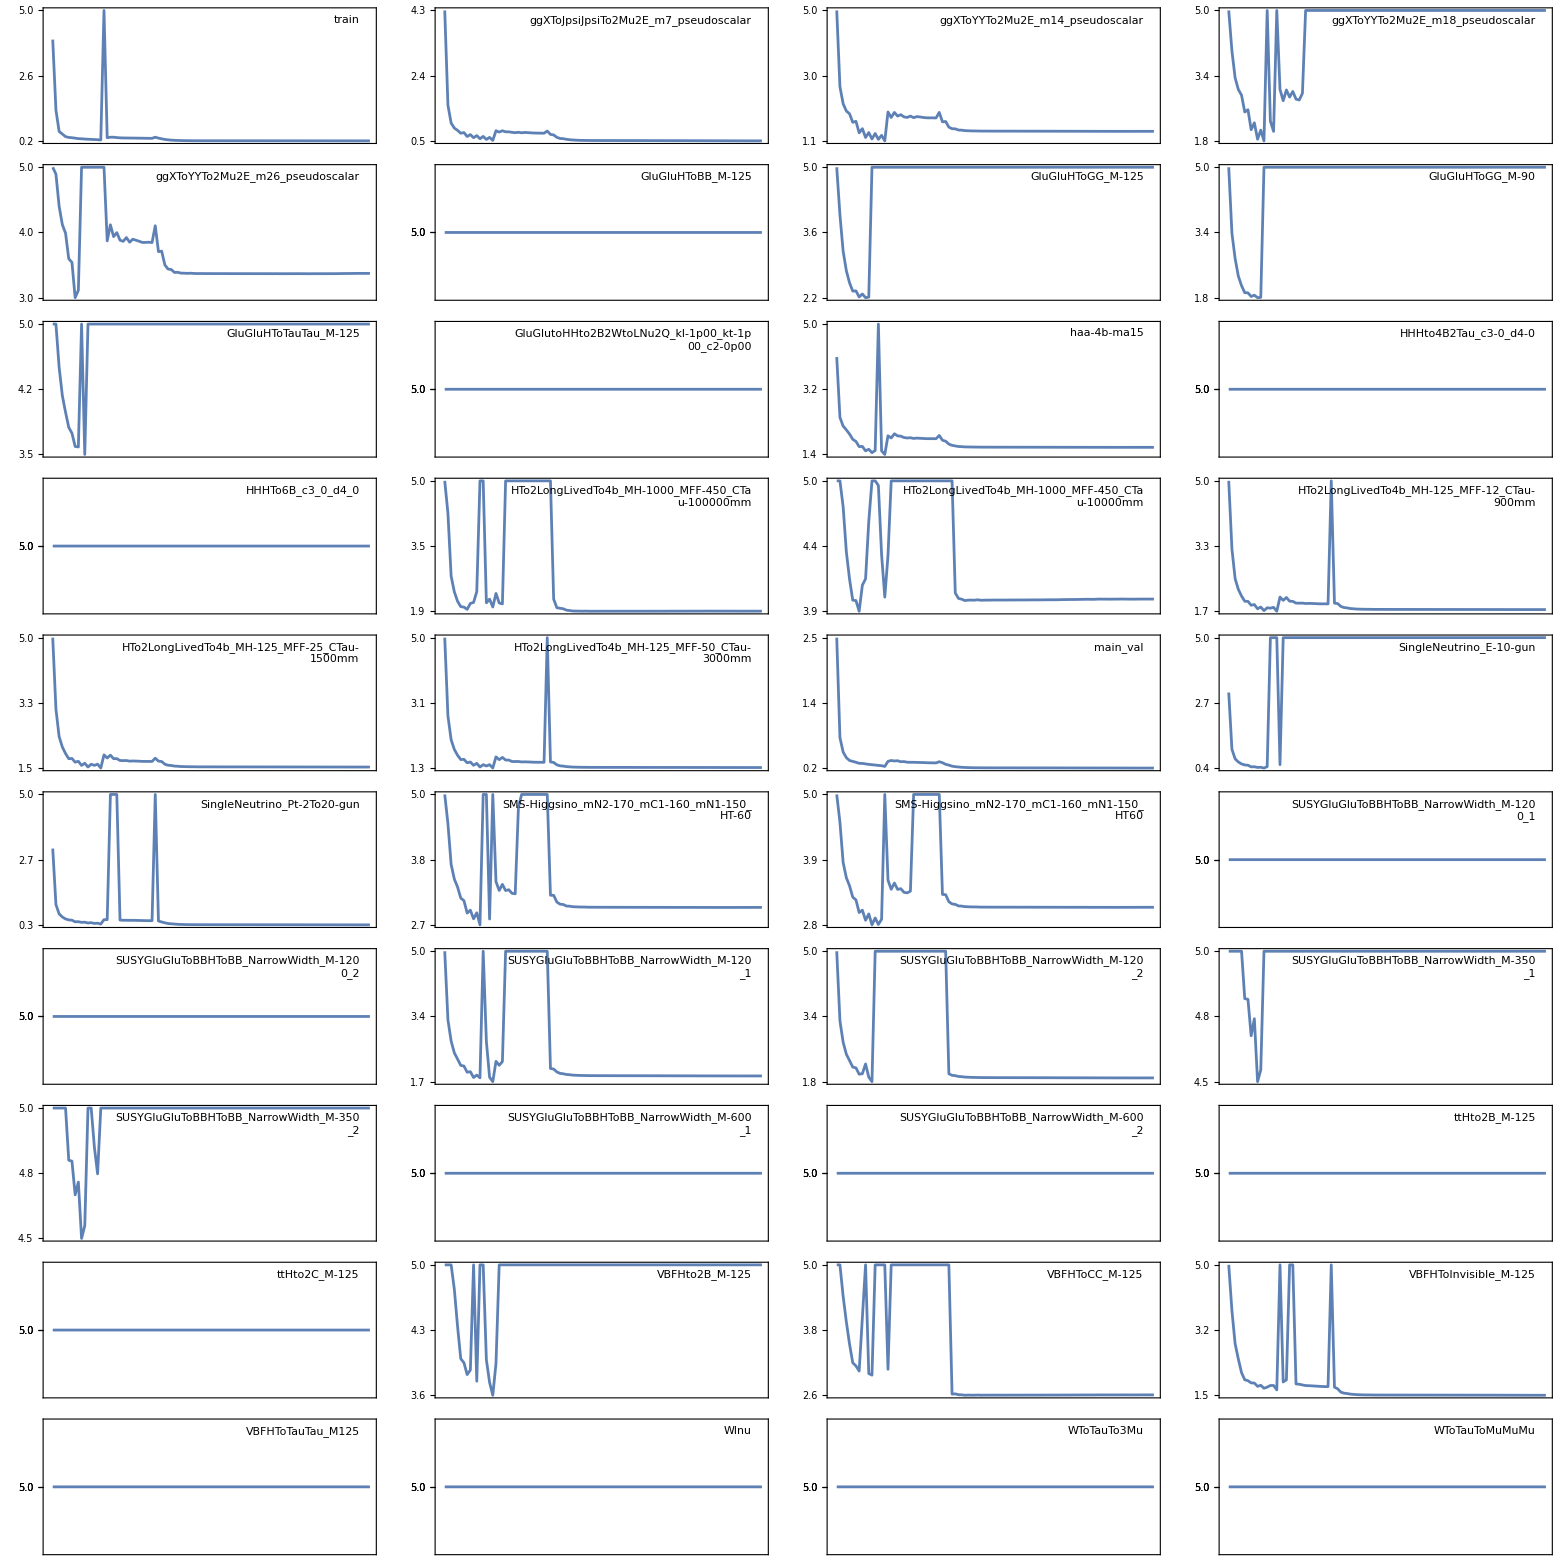
loss | -Graphics-
 | Epochs ∈ [0, 100]

```mathematica
makePlot[row_,label_]:=ListLinePlot[row,PlotStyle->{Medium},Axes->False,Frame->True,FrameTicks->{{{{Min[row],NumberForm[N[Min[row]],{5,1}]},{(Min[row]+(Max[row] - Min[row])/2),NumberForm[N[Min[row]+(Max[row] - Min[row])/2],{5,1}]},{Max[row],NumberForm[N[Max[row]],{5,1}]}},None},{None,None}},FrameTicksStyle->Directive[11,FontWeight->"Plain"],PlotRange->{All, {Min[row], Max[row]}},ImageSize->300,PlotLabel->None,Epilog->{Inset[Style[label,11,FontWeight->"Plain",Background->White],Scaled[{0.95,0.95}],{Right,Top}]}];
plots=MapThread[makePlot,{plotData,datasetNamesWrapped}];

possiblePartitions = Divisors[Length@datasetNames];
plotsPerRow = possiblePartitions[[4]];
grid=Partition[plots,4];

fullGridWithAxes=Grid[{{"",Grid[grid,Spacings->{1,1},Alignment->Center]},{"",Style["Epochs ∈ [0, 100]",FontWeight->"SemiBold",24, Gray]}},Spacings->{1,2}];
Row[{Style[Rotate[desiredMetric,90 Degree],FontWeight->"SemiBold",24, Gray],Spacer[10],fullGridWithAxes}]
```

```mathematica
Export["dataset_grids/" <>FileBaseName@desiredMetric <> "_" <>desiredRun <> ".png",%]
```

dataset_grids/loss_scan_lr0.001_alpha0.6.png

# Dynamic Plot

```mathematica
DynamicModule[{data,labels,lineSelection={},hovered=None},data=plotData;
labels=datasetNames;
(*Color function for selected lines*)colors=ColorData[97,"ColorList"];
colorFunc=Function[i,colors[[Mod[i-1,Length[colors]]+1]]];
Column[{Style["Select datasets to display:",Bold,16],Pane[CheckboxBar[Dynamic[lineSelection],labels,Appearance->"Vertical"],{500,200},Scrollbars->True],Row[{Button["Clear Selection",(lineSelection={};hovered=None;),ImageSize->Medium],Button["Select All",(lineSelection=labels;),ImageSize->Medium]}],Dynamic[Module[{selectedIndices,selectedColors,plot,overlay,legend},selectedIndices=Flatten@Position[labels,_?(MemberQ[lineSelection,#]&)];
selectedColors=AssociationThread[lineSelection->Table[colorFunc[i],{i,Length[lineSelection]}]];
plot=ListLinePlot[data[[selectedIndices]],PlotStyle->MapIndexed[Module[{lbl=labels[[selectedIndices[[First[#2]]]]],idx=First[#2]},Which[hovered===idx,{Thick,Red},MemberQ[lineSelection,lbl],{Thickness[0.0025],selectedColors[lbl],Opacity[0.7]},True,{Thickness[0.0015],Gray,Opacity[0.5]}]]&,Range[Length[selectedIndices]]],PlotRange->All,Axes->False,Frame->True,FrameTicksStyle->Directive[20],FrameLabel->{Style["Epochs",FontSize->24,Bold],Style[desiredMetric,FontSize->24,Bold]},ImageSize->{1800,1200},ImagePadding->120,PlotLegends->None];
overlay=Graphics[MapIndexed[With[{idx=First[#2],lbl=labels[[selectedIndices[[First[#2]]]]]},EventHandler[Tooltip[Invisible@Line[Transpose[{Range[Length[#1]],#1}]],lbl,TooltipStyle->Directive[16,Red,Bold]],{"MouseEntered":>(hovered=idx),"MouseExited":>(hovered=None),"MouseClicked":>(If[MemberQ[lineSelection,lbl],lineSelection=DeleteCases[lineSelection,lbl],AppendTo[lineSelection,lbl]])}]]&,data[[selectedIndices]]]];
legend=If[lineSelection==={},"",SwatchLegend[Values[selectedColors],Keys[selectedColors],LegendMarkerSize->20,LabelStyle->Directive[20]]];
Show[plot,overlay,Epilog->Inset[legend,Scaled[{0.98,0.98}],{Right,Top}]]]]}]]
```